```mathematica
Exit[]
```

#### Utilities & Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};
Comb5={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
Comb6={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"Palatino"],α Degree],Scaled[{x,y}]]
```

# QNMs of Halo Black Holes

```mathematica
(*Quit*)
```

```mathematica
(* non grid-based interpolation scheme to calculate QNMs of Schwarzschild black holes, I may have modified their method a bit. 
A HUGE CAUTION: any number you use has to be Rationalized or for large amount of grid points the code fail to work due to the differentiation matrices obtaining zero values*)
(* Main method taken from [arxiv:1610.08135v4] *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
n=15;
```

#### Differentiation matrices from built-in finite difference Mathematica functions

```mathematica
(*The above commented out code also calculates the differentiation matrices in the range we want but takes more time. It might be more accurate later when we deal with dirty black holes but for Schwarzschild the following method is enough.*)
min=0;
max=1;
 (*number of grid points used to discretize the metric components of spacetime, the compactified radial coordinate [0,1] and build the differentiation matrices*)
di=(max-min)/(n-1);(*equispaced data points*)
x=Table[i,{i,min,max,di}];
DF0=NDSolve`FiniteDifferenceDerivative[Derivative[0],Range[0,1,1/(n-1)],DifferenceOrder->n]["DifferentiationMatrix"] ;(*zeroth derivative*)
DF1=NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[0,1,1/(n-1)],DifferenceOrder->n-1]["DifferentiationMatrix"]; (*first derivative*)
DF2=NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[0,1,1/(n-1)],DifferenceOrder->n-2]["DifferentiationMatrix"]; (*second derivative*)
```

```mathematica
(* I delete the first and last entry in order to avoid calculating the functions at the extrema of the domain: 0 (rh) and 1 (∞), which are singular points *)
Delete[DF0,{{1},{n}}];
df0=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF1,{{1},{n}}];
df1=Delete[Transpose[%],{{1},{n}}]//Transpose;
Delete[DF2,{{1},{n}}];
df2=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

## l = 2

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,rc,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;
rc=5*a0;

ρmetric=background["NFW",M,{a0,rc},10^13][[1,{1,3}]];

f[r_]=(*(1-2/r)(1+(2 M)/(a0+2));*)ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=(*(1-2z)/rh;*)f'[rh];
derrmh=(D[ρprofile[r,M,{a0,rc},"NFW"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

(*ωtrial=SetPrecision[0.37-0.08I,50];*)

FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];

sol=FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

```mathematica
(*dataNl2Vac={0,0.3736713109133917,-0.08897500434877946};
dataNl3Vac={0,0.5994432884,-0.09270304794};
dataNl4Vac={0,0.8091783775,-0.09416396099};*)
```

```mathematica
dataNl2Vac=δω[0,2,29,SetPrecision[0.374-0.089I,50]];
```

```mathematica
dataNl3Vac=δω[0,3,22,SetPrecision[0.599-0.092I,50]];
```

```mathematica
dataNl4Vac=δω[0,4,19,SetPrecision[0.809-0.094I,50]];
```

```mathematica
dataNl2=Monitor[Table[δω[10^compactness[[ii]],2,29,SetPrecision[0.374-0.089I,50]],{ii,1,Length[compactness]}],ii];
```

$Aborted

```mathematica
dataNl3=Monitor[Table[δω[10^compactness[[ii]],3,22,SetPrecision[0.599-0.092I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
dataNl4=Monitor[Table[δω[10^compactness[[ii]],4,19,SetPrecision[0.809-0.094I,50]],{ii,1,Length[compactness]}],ii];
```

```mathematica
dataNl2T=Join[{dataNl2Vac},dataNl2];
dataNl3T=Join[{dataNl3Vac},dataNl3];
dataNl4T=Join[{dataNl4Vac},dataNl4];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
line2R=Fit[datasetR[dataNl2T,10^-2],{1,t,t^2},t]
line3R=Fit[datasetR[dataNl3T,10^-2],{1,t,t^2},t]
line4R=Fit[datasetR[dataNl4T,10^-2],{1,t,t^2},t]
```

2.8810610132940453970927849239241739531582605×10^-7+0.85674007869899700409057883383318503561048866 t-6.0970626823648394781211349795097733850545111 t^2

3.3324237881209262568691700459964476086650673×10^-8+0.79478688811716227962091752351468139308704504 t-0.85057521263272232151979174685809924183383814 t^2

1.35697728657510453464806800654301885985356345×10^-7+0.80928613645635643776440212937446028852455219 t-1.28647007558318242720240978654220565878985618 t^2

```mathematica
26,13
```

1.6040349504730256936951309591589559370671161×10^-7+0.81436182335194212973518639032754912539690126 t-2.2343211283081343377661408999670034984581184 t^2

2.1309093895429294271730942593594272994770061×10^-7+0.73894069878198331141107783726482443019238447 t-0.39473227393828442936671117708598482650249922 t^2

1.43613007992954516355909656510447724430516213×10^-7+0.784987372470877078569624129485728305445449972 t-1.08317868464670519231070862078374181376426245 t^2

```mathematica
line2I=Fit[datasetI[dataNl2T,10^-2],{1,t,t^2},t]
line3I=Fit[datasetI[dataNl3T,10^-2],{1,t,t^2},t]
line4I=Fit[datasetI[dataNl4T,10^-2],{1,t,t^2},t]
```

-9.8422137892949559021170818093389330844879473×10^-6+1.0213593230047706035194403436371850901720511 t-3.6318205685019495272550304548667571514420053 t^2

-1.5453517933639209272859168395350959930545757×10^-6+1.0084783732530507636806315206927493395351728 t-9.3077552389562900501830904254808992677911608 t^2

-2.25872879871367415819709142104977533987808652×10^-6+1.09260026165096890880269924137535141904988814 t-8.74733339876504430959781410233948097016274032 t^2

```mathematica
26, 13
```

-4.4701409873666029518269541181344498152998499×10^-6+0.85255266462195064483980654623918074095689112 t-3.6520408154476804319226240989007177588235041 t^2

-4.3601977516527994496824498682625424365680929×10^-8+1.0850602323023146606660844458991648336219511 t-13.114788589862324324619854083473865617039462 t^2

-1.20844593669008328221560884200153939767143534×10^-6+1.14578831699190925131461010488802315104565227 t-8.14988864214768533378068029885607961782885113 t^2

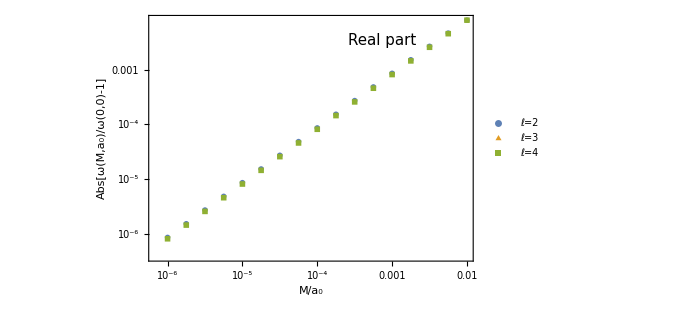

```mathematica
p1=ListLogLogPlot[{
datasetR[dataNl2T,10^-2],
datasetR[dataNl3T,10^-2],
datasetR[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.72,0.9,Black]}]
(*Export["./plot/realZ_N_MM.pdf",%]*)
```

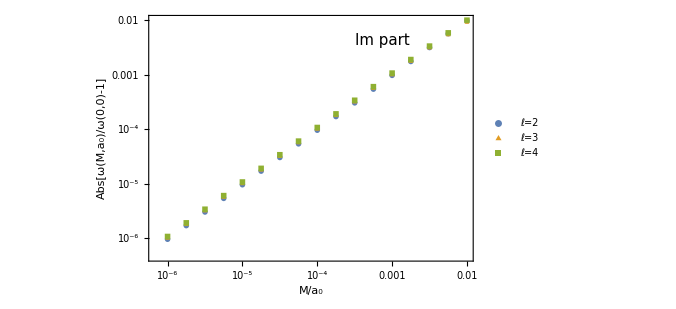

```mathematica
p2=ListLogLogPlot[{
datasetI[dataNl2T,10^-2],
datasetI[dataNl3T,10^-2],
datasetI[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.72,0.9,Black]}]
(*Export["./plot/imZ_N_MM.pdf",%]*)
```

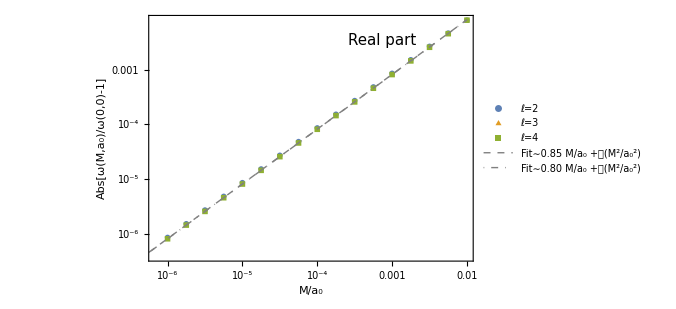

./plot/realZ_N_MM_fit.pdf

```mathematica
Show[p1,LogLogPlot[{0.8143618233519421297351863903275491253969012577807371854032`44.31328241345991 t,0.8092861364563564377644021293744602885245521903246797309652`45.23302622526928 t},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.85 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼0.80 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_N_MM_fit.pdf",%]
```

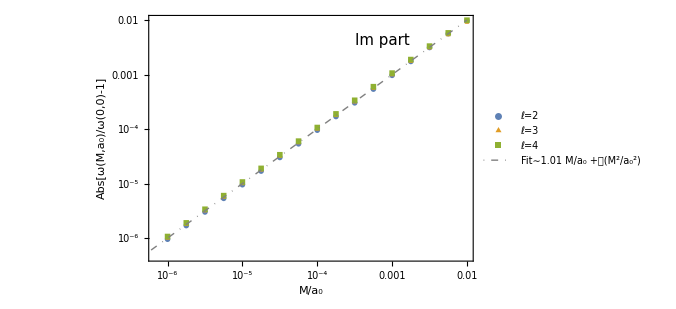

./plot/imZ_N_MM_fit.pdf

```mathematica
Show[p2,LogLogPlot[{1.0084783732530507636806315206927493395351727660552565141722`44.4474328247178 t},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed, AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼1.01 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit∼1. M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_N_MM_fit.pdf",%]
```

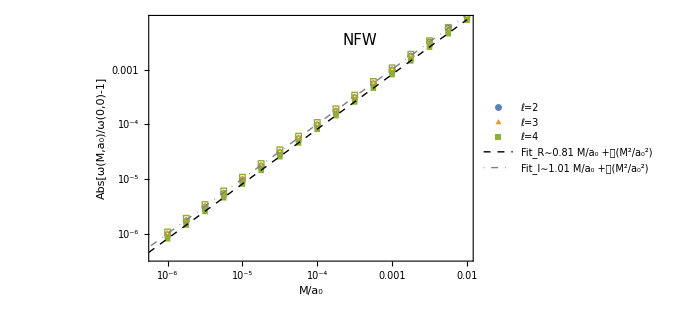

./plot/allZ_N_MM_fit.pdf

```mathematica
p1V=ListLogLogPlot[{
datasetR[dataNl2T,10^-2],
datasetR[dataNl3T,10^-2],
datasetR[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["NFW",15,0,0.65,0.9,Black]}];
p2V=ListLogLogPlot[{
datasetI[dataNl2T,10^-2],
datasetI[dataNl3T,10^-2],
datasetI[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotMarkers->{{○,Large},{△,Medium},{□,Small}}];
Show[p1V,p2V,LogLogPlot[{0.8143618233519421297351863903275491253969012577807371854032`44.31328241345991 t,1.0084783732530507636806315206927493395351727660552565141722`44.4474328247178 t},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,Dashed,AbsoluteThickness[1]],Directive[Gray,DotDashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.81 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼1.01 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/allZ_N_MM_fit.pdf",%]
```

```mathematica
Export["Matrix_NFW.m",{dataNl2T,dataNl3T, dataNl4T}]
```

Matrix_NFW.m